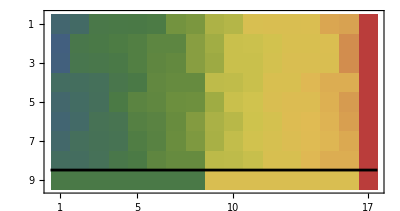

{{0.,0.,1.,1.,0.,1.,1.,0.,0.,0.,1.,0.,0.,1.,0.,1.,1.},{0.,0.,0.,1.,1.,1.,0.,1.,1.,0.,0.,1.,1.,1.,0.,0.,0.},{1.,0.,0.,1.,0.,0.,1.,0.,1.,1.,0.,0.,1.,1.,0.,0.,1.},{1.,1.,1.,0.,0.,0.,0.,1.,0.,1.,1.,0.,1.,0.,1.,0.,0.},{0.,1.,0.,0.,0.,0.,1.,1.,0.,1.,0.,0.,1.,0.,1.,1.,1.},{1.,1.,0.,0.,0.,0.,1.,1.,0.,1.,1.,1.,0.,1.,0.,0.,0.},{1.,0.,1.,0.,1.,1.,0.,0.,0.,1.,0.,1.,1.,0.,0.,0.,1.},{0.,1.,0.,1.,1.,1.,0.,0.,1.,1.,1.,0.,0.,0.,0.,1.,0.},{0.,1.,1.,0.,0.,0.,0.,1.,0.,1.,0.,1.,0.,1.,0.,1.,1.},{0.,0.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.,0.,0.,1.,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,1.,1.,1.},{0.,1.,0.,0.,0.,1.,1.,0.,1.,0.,1.,0.,1.,0.,1.,0.,1.},{0.,1.,1.,1.,1.,0.,1.,0.,0.,0.,0.,1.,0.,1.,1.,0.,0.},{1.,1.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,1.,0.,1.,1.,0.},{0.,0.,0.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.,1.,0.,1.,0.},{1.,0.,0.,0.,1.,0.,0.,1.,1.,0.,1.,0.,0.,1.,1.,0.,1.},{1.,0.,1.,0.,1.,0.,1.,0.,1.,0.,1.,1.,0.,0.,0.,1.,0.}}

```mathematica
Localmin=BinaryReadList["UU/Scriptie//localmin44_17.dat", "Real32"];
Graphsize = 17;
Size = Length[Localmin]/(Graphsize^2);
Length[Localmin];
Totaleigs = Table[n, {n, Size}];
Totaleigs=Map[Function[i, Sort[N[Eigenvalues[ArrayReshape[Localmin[[(i-1)*Graphsize^2+1;;i*Graphsize^2]], {Graphsize, Graphsize}]]]]], Totaleigs];
G=Import["Grafencollectie//r44_17.g6"];
Totaleigs = Append[Totaleigs, Sort[N[Eigenvalues[AdjacencyMatrix[G]]]]];
Show[MatrixPlot[Totaleigs, ColorFunction -> "DarkRainbow"],Plot[1, {x, 0, 17}, PlotStyle-> Black]]

Graph1 = ArrayReshape[Localmin[[1;;Graphsize^2]], {Graphsize, Graphsize}]
```